## Data opening

```mathematica
Vibrio=Import[NotebookDirectory[]<>"Vibrio.csv"];
Ecoli=Import[NotebookDirectory[]<>"Ecoli.csv"];
CSAlginate=Import[NotebookDirectory[]<>"CSAlginate.csv"];
Acetate=Import[NotebookDirectory[]<>"Acetate.csv"];
HP=Import[NotebookDirectory[]<>"3HP.csv"];
```

```mathematica
Acetatedata100=Table[{Acetate[[i,1]],(Acetate[[i,2]]+Acetate[[i,3]])/2},{i,2,Length[Acetate]}];
Acetatedata112=Table[{Acetate[[i,1]],(Acetate[[i,4]]+Acetate[[i,5]])/2},{i,2,Length[Acetate]}];
Acetatedata119=Table[{Acetate[[i,1]],(Acetate[[i,6]]+Acetate[[i,7]])/2},{i,2,Length[Acetate]}];
Acetatedata109=Table[{Acetate[[i,1]],(Acetate[[i,8]]+Acetate[[i,9]])/2},{i,2,Length[Acetate]}];
```

```mathematica
HPdata100=Table[{HP[[i,1]],(HP[[i,2]]+HP[[i,3]])/2},{i,2,Length[HP]}];
HPdata112=Table[{HP[[i,1]],(HP[[i,4]]+HP[[i,5]])/2},{i,2,Length[HP]}];
HPdata119=Table[{HP[[i,1]],(HP[[i,6]]+HP[[i,7]])/2},{i,2,Length[HP]}];
HPdata109=Table[{HP[[i,1]],(HP[[i,8]]+HP[[i,9]])/2},{i,2,Length[HP]}];
```

```mathematica
Vibriodata100=Table[{Vibrio[[i,1]],(Vibrio[[i,2]]+Vibrio[[i,3]])/2},{i,2,Length[Vibrio]}];
Vibriodata112=Table[{Vibrio[[i,1]],(Vibrio[[i,4]]+Vibrio[[i,5]])/2},{i,2,Length[Vibrio]}];
Vibriodata119=Table[{Vibrio[[i,1]],(Vibrio[[i,6]]+Vibrio[[i,7]])/2},{i,2,Length[Vibrio]}];
Vibriodata109=Table[{Vibrio[[i,1]],(Vibrio[[i,8]]+Vibrio[[i,9]])/2},{i,2,Length[Vibrio]}];
```

```mathematica
Vibinter100=Interpolation[Table[{Vibrio[[i,1]],(Vibrio[[i,2]]+Vibrio[[i,3]])/2},{i,2,Length[Vibrio]}],InterpolationOrder->1];
Vibinter112=Interpolation[Table[{Vibrio[[i,1]],(Vibrio[[i,4]]+Vibrio[[i,5]])/2},{i,2,Length[Vibrio]}],InterpolationOrder->1];
Vibinter119=Interpolation[Table[{Vibrio[[i,1]],(Vibrio[[i,6]]+Vibrio[[i,7]])/2},{i,2,Length[Vibrio]}],InterpolationOrder->1];
Vibinter109=Interpolation[Table[{Vibrio[[i,1]],(Vibrio[[i,8]]+Vibrio[[i,9]])/2},{i,2,Length[Vibrio]}],InterpolationOrder->1];
```

```mathematica
Ecolidata100=Table[{Ecoli[[i,1]],(Ecoli[[i,2]]+Ecoli[[i,3]])/2},{i,2,Length[Ecoli]}];
Ecolidata112=Table[{Ecoli[[i,1]],(Ecoli[[i,4]]+Ecoli[[i,5]])/2},{i,2,Length[Ecoli]}];
Ecolidata119=Table[{Ecoli[[i,1]],(Ecoli[[i,6]]+Ecoli[[i,7]])/2},{i,2,Length[Ecoli]}];
Ecolidata109=Table[{Ecoli[[i,1]],(Ecoli[[i,8]]+Ecoli[[i,9]])/2},{i,2,Length[Ecoli]}];
```

```mathematica
Ecoliinter100=Interpolation[Ecolidata100,InterpolationOrder->3,InterpolationOrder->1];
Ecoliinter112=Interpolation[Ecolidata112,InterpolationOrder->1,InterpolationOrder->1];
Ecoliinter119=Interpolation[Ecolidata119,InterpolationOrder->1,InterpolationOrder->1];
Ecoliinter109=Interpolation[Ecolidata109,InterpolationOrder->1,InterpolationOrder->1];
```

```mathematica
CSAlginatedata100=Table[{CSAlginate[[i,1]],(CSAlginate[[i,2]]+CSAlginate[[i,3]])/2},{i,2,Length[CSAlginate]}];
CSAlginatedata112=Table[{CSAlginate[[i,1]],(CSAlginate[[i,4]]+CSAlginate[[i,5]])/2},{i,2,Length[CSAlginate]}];
CSAlginatedata119=Table[{CSAlginate[[i,1]],(CSAlginate[[i,6]]+CSAlginate[[i,7]])/2},{i,2,Length[CSAlginate]}];
CSAlginatedata109=Table[{CSAlginate[[i,1]],(CSAlginate[[i,8]]+CSAlginate[[i,9]])/2},{i,2,Length[CSAlginate]}];
```

```mathematica
FindFit[Ecolidata100,(a+b t+c t^2)/(e+f t+g t^2)+2.10936,{a,b,c,e,f,g},t]
```

{a→150.18,b→830.487,c→-13.8258,e→974.799,f→26.9828,g→-0.602892}

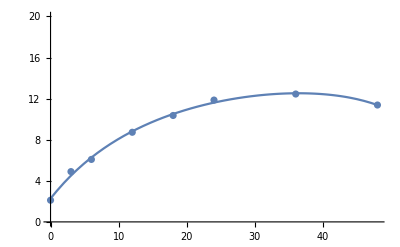

```mathematica
Show[Plot[(150.1795637864267+830.4874240802603 t-13.825830741440214 t^2)/(974.7992466446619+26.98281037012016 t-0.6028923751671911 t^2)+2.10936,{t,0,48},PlotRange->{0,20}],ListPlot[Ecolidata100]]
```

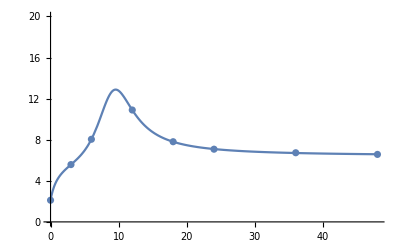

```mathematica
Show[Plot[(-13531.624264126762-32224.628643116666 t+6273.5868493553935 t^2-396.4644964549835 t^3)/(-6415.053187355805-4226.688104113332t+1024.0154751309897 t^2-61.93526821053972 t^3),{t,0,48},PlotRange->{0,20}],ListPlot[Ecolidata112]]
```

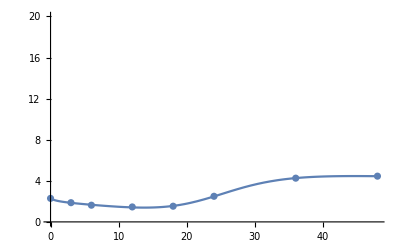

```mathematica
Show[Plot[(42.32363338450361+28.501920754636863 t-2.6410617317999288t^2+0.0786036694879362t^3)/(18.478799348237292+15.797701140831474t-1.0271850497014503 t^2+0.022545319014934485 t^3),{t,0,48},PlotRange->{0,20}],ListPlot[Ecolidata119]]
```

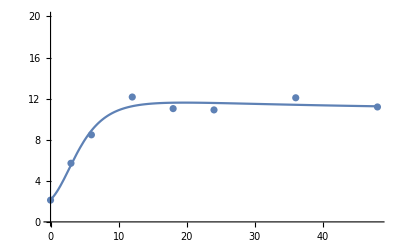

```mathematica
Show[Plot[(702.7780370589741+182.39818319098484t+83.8511381596518t^2)/(325.1354708176569-11.264847942814695t+7.909544725823299t^2),{t,0,48},PlotRange->{0,20}],ListPlot[Ecolidata109]]
```

```mathematica
Ecoliint100[t_]:=(150.1795637864267+830.4874240802603 t-13.825830741440214 t^2)/(974.7992466446619+26.98281037012016 t-0.6028923751671911 t^2)+2.10936
Ecoliint112[t_]:=(-13531.624264126762-32224.628643116666 t+6273.5868493553935 t^2-396.4644964549835 t^3)/(-6415.053187355805-4226.688104113332t+1024.0154751309897 t^2-61.93526821053972 t^3)
Ecoliint119[t_]:=(42.32363338450361+28.501920754636863 t-2.6410617317999288t^2+0.0786036694879362t^3)/(18.478799348237292+15.797701140831474t-1.0271850497014503 t^2+0.022545319014934485 t^3)
Ecoliint109[t_]:=(702.7780370589741+182.39818319098484t+83.8511381596518t^2)/(325.1354708176569-11.264847942814695t+7.909544725823299t^2)
```

```mathematica
FindFit[CSAlginatedata100,(a+b t+c t^2+d t^3)/(e+f t+g t^2+h t^3),{a,b,c,d,e,f,g,h},t]
```

{a→3035.92,b→7.97817×10^6,c→-1.17511×10^6,d→58202.3,e→2.3838×10^6,f→154270.,g→-47321.3,h→2876.78}

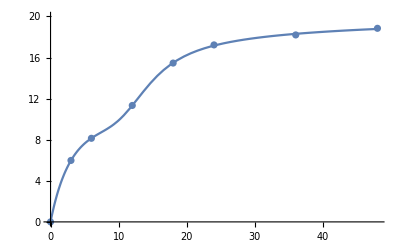

```mathematica
Show[Plot[(3035.9167675934286+7.978168660225129*^6 t-1.1751072202406772*^6 t^2+58202.31556831093t^3)/(2.38379870099275*^6+154270 t-47321.29335678422 t^2+2876.77979221488t^3),{t,0,48},PlotRange->{0,20}],ListPlot[CSAlginatedata100]]
```

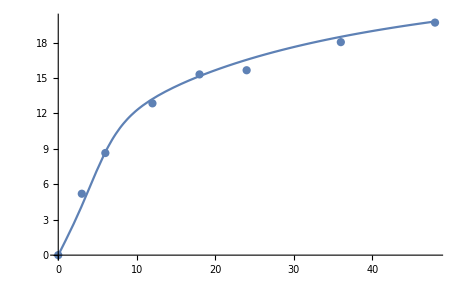

```mathematica
Show[Plot[(-0.08570381293135143+83.60502249019599t-11.233509385750217 t^2+1.8087463701269082 t^3)/(63.14527037836695-7.958478217294559 t+0.7089946994786837 t^2+0.06954894535439794 t^3),{t,0,48},PlotRange->{0,20}],ListPlot[CSAlginatedata112]]
```

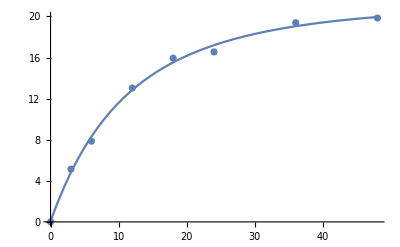

```mathematica
Show[Plot[(6.915793303398713+227.68191575079393 t+4.444542312745424 t^2)/(121.70551344241632+9.181153002280578 t+0.21665273968397145 t^2),{t,0,48},PlotRange->{0,20}],ListPlot[CSAlginatedata119]]
```

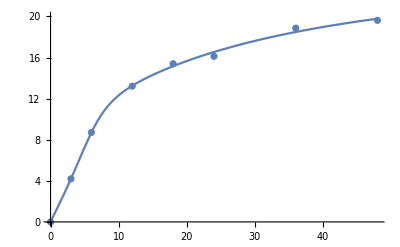

```mathematica
Show[Plot[(-0.20993579378014796+189.2341117860539t-28.725947074945037t^2+3.786027793502709t^3)/(136.53259025420482-17.813922646484755t+1.2326642046386984t^2+0.14610664330942674t^3),{t,0,48},PlotRange->{0,20}],ListPlot[CSAlginatedata109]]
```

```mathematica
CSAli100[t_]:=(3035.9167675934286+7.978168660225129*^6 t-1.1751072202406772*^6 t^2+58202.31556831093t^3)/(2.38379870099275*^6+154270 t-47321.29335678422 t^2+2876.77979221488t^3)
CSAli112[t_]:=(-0.08570381293135143+83.60502249019599t-11.233509385750217 t^2+1.8087463701269082 t^3)/(63.14527037836695-7.958478217294559 t+0.7089946994786837 t^2+0.06954894535439794 t^3)
CSAli119[t_]:=(6.915793303398713+227.68191575079393 t+4.444542312745424 t^2)/(121.70551344241632+9.181153002280578 t+0.21665273968397145 t^2)
CSAli109[t_]:=(-0.20993579378014796+189.2341117860539t-28.725947074945037t^2+3.786027793502709t^3)/(136.53259025420482-17.813922646484755t+1.2326642046386984t^2+0.14610664330942674t^3)
```

## Acetate-3HP

```mathematica
Ace1001=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter100[t]-c Ac[t]/(d+Ac[t])Vibinter100[t] 1/(1+Exp[-1(t-32)])+0.2CSAli100'[t],Ac[0]==0},Ac,{t,0,48},{a,K,c,d}];
Ace1191=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter119[t]-c Ac[t]/(d+Ac[t])Vibinter119[t] 1/(1+Exp[-1(t-24)])+0.2CSAli119'[t],Ac[0]==0},Ac,{t,0,48},{a,K,c,d}];
Ace1121=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter112[t]-c Ac[t]/(d+Ac[t])Vibinter112[t] 1/(1+Exp[-1(t-32)])+0.2CSAli112'[t],Ac[0]==0},Ac,{t,0,48},{a,K,c,d}];
Ace1091=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter109[t]-c Ac[t]/(d+Ac[t])Vibinter109[t] 1/(1+Exp[-1(t-32)])+0.2CSAli109'[t],Ac[0]==0},Ac,{t,0,48},{a,K,c,d}];
```

```mathematica
Ace100Econly=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter100[t]+0.2CSAli100'[t],Ac[0]==0},Ac,{t,0,48},{a,K}];
Ace119Econly=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter119[t]+0.2CSAli119'[t],Ac[0]==0},Ac,{t,0,48},{a,K}];
Ace112Econly=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter112[t]+0.2CSAli112'[t],Ac[0]==0},Ac,{t,0,48},{a,K}];
Ace109Econly=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter109[t]+0.2CSAli109'[t],Ac[0]==0},Ac,{t,0,48},{a,K}];
```

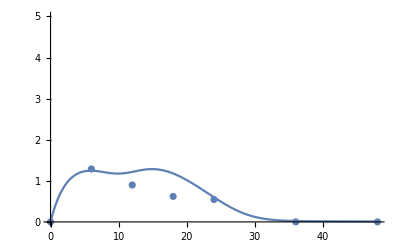

```mathematica
Show[Plot[Ace1001[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t],{t,0,48},PlotRange->{0,5}],ListPlot[Acetatedata100]]
```

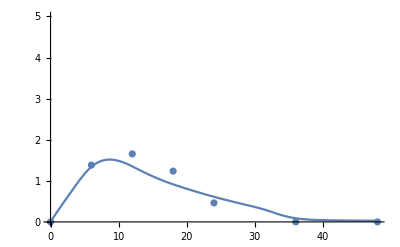

```mathematica
Show[Plot[Ace1121[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t],{t,0,48},PlotRange->{0,5}],ListPlot[Acetatedata112]]
```

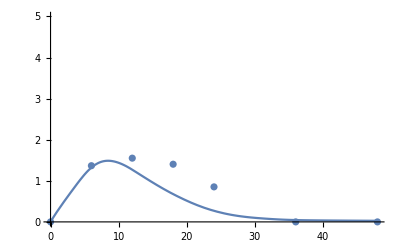

```mathematica
Show[Plot[Ace1091[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t],{t,0,48},PlotRange->{0,5}],ListPlot[Acetatedata109]]
```

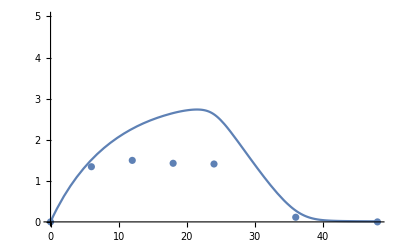

```mathematica
Show[Plot[Ace1191[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t],{t,0,48},PlotRange->{0,5}],ListPlot[Acetatedata119]]
```

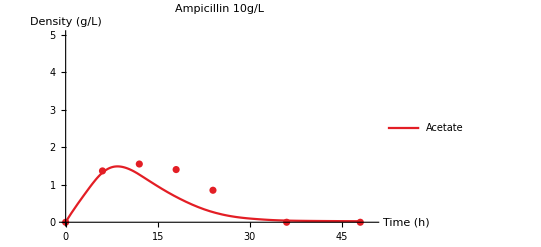

```mathematica
Show[Plot[Ace1091[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t],{t,0,48},PlotRange->{{0,50},{0,5.0}},PlotLegends->{"Acetate","3-HP","ampicillin 10μg/mL","ampicillin 20μg/mL"},PlotLabel->Style["
Ampicillin 10g/L",Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256]}],ListPlot[{Acetatedata109},PlotRange->{{0,50},{0,5}},Joined->False,PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256]}]]
```

```mathematica
CSAce100[t_]:=0.2CSAli100[t]-Ace100Econly[0.01999654485115207,0.40513230161658544][t]
CSAce112[t_]:=0.2CSAli112[t]-Ace112Econly[0.01999654485115207,0.40513230161658544][t]
CSAce119[t_]:=0.2CSAli119[t]-Ace119Econly[0.01999654485115207,0.40513230161658544][t]
CSAce109[t_]:=0.2CSAli109[t]-Ace109Econly[0.01999654485115207,0.40513230161658544][t]
```

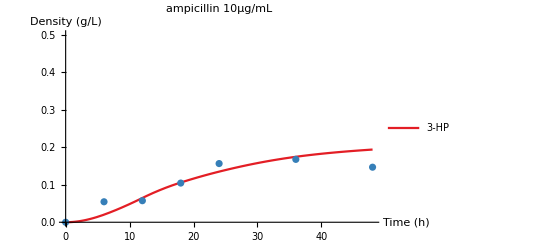

```mathematica
Show[Plot[0.05CSAce112[t],{t,0,48},PlotRange->{0,0.5},PlotLegends->{"3-HP","3-HP","ampicillin 10μg/mL","ampicillin 20μg/mL"},PlotLabel->Style["
ampicillin 10μg/mL",Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256]}],ListPlot[Table[{HPdata112[[i,1]],HPdata112[[i,2]]},{i,1,Length[HPdata100]}],PlotRange->{{0,50},{0,5}},Joined->False,PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256]}]]
```

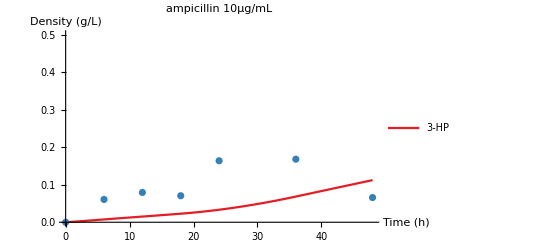

```mathematica
Show[Plot[0.05CSAce119[t],{t,0,48},PlotRange->{0,0.5},PlotLegends->{"3-HP","3-HP","ampicillin 10μg/mL","ampicillin 20μg/mL"},PlotLabel->Style["
ampicillin 10μg/mL",Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256]}],ListPlot[Table[{HPdata119[[i,1]],HPdata119[[i,2]]},{i,1,Length[HPdata119]}],PlotRange->{{0,50},{0,5}},Joined->False,PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256]}]]
```

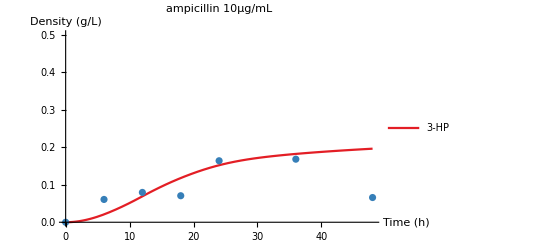

```mathematica
Show[Plot[0.05CSAce109[t],{t,0,48},PlotRange->{0,0.5},PlotLegends->{"3-HP","3-HP","ampicillin 10μg/mL","ampicillin 20μg/mL"},PlotLabel->Style["
ampicillin 10μg/mL",Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256]}],ListPlot[Table[{HPdata112[[i,1]],HPdata119[[i,2]]},{i,1,Length[HPdata100]}],PlotRange->{{0,50},{0,5}},Joined->False,PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256]}]]
```

## Ecoli

```mathematica
EcoliFit119=ParametricNDSolveValue[{EM'[t]==a*CSAce119'[t]-kd EM[t],EM[0]==2.10936},EM,{t,0,48},{a,kd}];
```

```mathematica
Ec119[a_?NumberQ,kd_?NumberQ]:=(EcM0[a,kd]=First[EM/.NDSolve[{EM'[t]==a*CSAce119'[t]-kd EM[t],EM[0]==2.10936},EM,{t,0,48}]]);
```

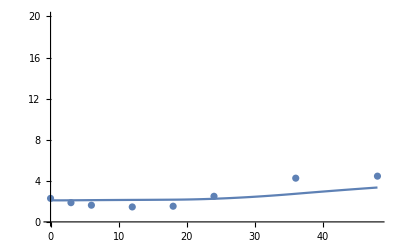

```mathematica
Show[Plot[EcoliFit119[1.24,0.013][t],{t,0,48},PlotRange->{0,20}],ListPlot[Ecolidata119]]
```

```mathematica
EcoliFit109=ParametricNDSolveValue[{EM'[t]==a*CSAce109'[t]-kd EM[t],EM[0]==2.10936},EM,{t,0,48},{a,kd}];
```

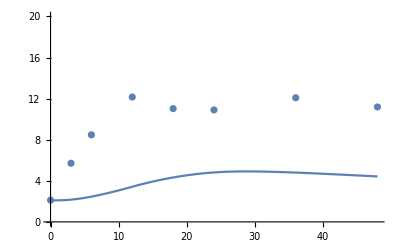

```mathematica
Show[Plot[EcoliFit109[1.24,0.013][t],{t,0,48},PlotRange->{0,20}],ListPlot[Ecolidata109]]
```

```mathematica
EcoliFit112=ParametricNDSolveValue[{EM'[t]==a*CSAce112'[t]-kd EM[t],EM[0]==2.10936},EM,{t,0,48},{a,kd}];
```

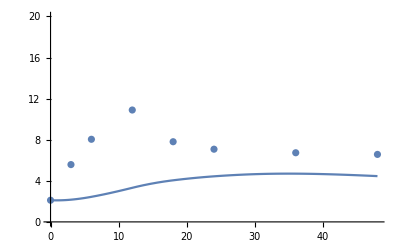

```mathematica
Show[Plot[EcoliFit112[1.24,0.013][t],{t,0,48},PlotRange->{0,20}],ListPlot[Ecolidata112]]
```

```mathematica
Amp10=ParametricNDSolveValue[{Amp'[t]==-ka Amp[t]/(Amp[t]+Ka)Ecoliinter119[t],Amp[0]==10},Amp,{t,0,48},{ka,Ka}];
```

```mathematica
VibrioFit119=ParametricNDSolveValue[{VM'[t]==0.97*CSAli119'[t]+0.015(Ace1191[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t])/(0.40513230161658544+Ace1191[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t])VM[t] 1/(1+Exp[-1(t-24)])-0.0104 VM[t]-0.05(Amp10[a,b][t])/(0.5+Amp10[a,b][t])VM[t],VM[0]==0.5725},VM,{t,0,48},{a,b}];
```

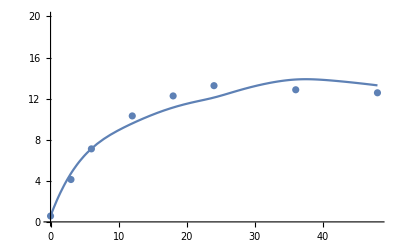

```mathematica
Show[Plot[VibrioFit119[1.4,5][t],{t,0,48},PlotRange->{0,20}],ListPlot[Vibriodata119]]
```

```mathematica
Amp10=ParametricNDSolveValue[{Amp'[t]==-ka Amp[t]/(Amp[t]+Ka)Ecoliinter100[t],Amp[0]==10},Amp,{t,0,48},{ka,Ka}];
```

```mathematica
VibrioFit100=ParametricNDSolveValue[{VM'[t]==0.97*CSAli100'[t]+0.015(Ace1001[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t])/(0.40513230161658544+Ace1001[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t])VM[t] 1/(1+Exp[-1(t-32)])-0.0104 VM[t]-0.14(Amp10[a,b][t])/(0.5+Amp10[a,b][t])VM[t],VM[0]==0.5725},VM,{t,0,48},{a,b}];
```

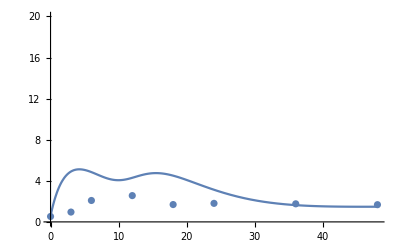

```mathematica
Show[Plot[VibrioFit100[0.08,5][t],{t,0,48},PlotRange->{0,20}],ListPlot[Vibriodata100]]
```

```mathematica
Amp10=ParametricNDSolveValue[{Amp'[t]==-ka Amp[t]/(Amp[t]+Ka)Ecoliinter112[t],Amp[0]==10},Amp,{t,0,48},{ka,Ka}];
```

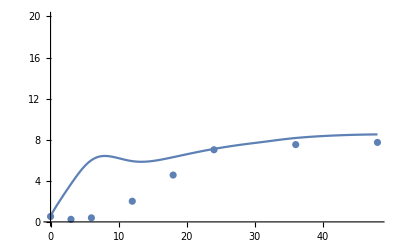

```mathematica
VibrioFit112=ParametricNDSolveValue[{VM'[t]==0.97*CSAli112'[t]+0.015(Ace1121[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t])/(0.40513230161658544+Ace1121[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t])VM[t] 1/(1+Exp[-1(t-32)])-0.0104 VM[t]-0.14(Amp10[a,b][t])/(0.5+Amp10[a,b][t])VM[t],VM[0]==0.5725},VM,{t,0,48},{a,b}];
Show[Plot[VibrioFit112[0.27,5][t],{t,0,48},PlotRange->{0,20}],ListPlot[Vibriodata112]]
```

```mathematica
Amp10=ParametricNDSolveValue[{Amp'[t]==-ka Amp[t]/(Amp[t]+Ka)Ecoliinter109[t],Amp[0]==10},Amp,{t,0,48},{ka,Ka}];
```

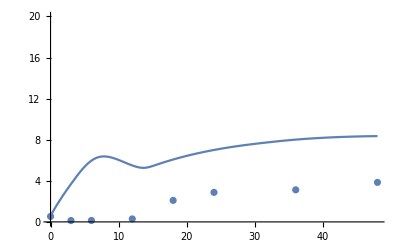

```mathematica
VibrioFit109=ParametricNDSolveValue[{VM'[t]==0.97*CSAli109'[t]+0.015(Ace1091[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t])/(0.40513230161658544+Ace1091[0.01999654485115207,0.40513230161658544,0.01999654485115207,0.40513230161658544][t])VM[t] 1/(1+Exp[-1(t-32)])-0.0104 VM[t]-0.14(Amp10[a,b][t])/(0.5+Amp10[a,b][t])VM[t],VM[0]==0.5725},VM,{t,0,48},{a,b}];
Show[Plot[VibrioFit109[0.10,0.5][t],{t,0,48},PlotRange->{0,20}],ListPlot[Vibriodata109]]
```